## Load chain

The example is analysis on the Planck chains (Planck+WP). Those chains can be downloaded at 
http://pla.esac.esa.int/pla/aio/product-action?COSMOLOGY.FILE_ID=COM_CosmoParams_base_planck_lowl_lowLike_R1.10.tar.gz

```mathematica
<<ChainStat.m
```

ChainStat, by Yi Wang (2014, GPLv3). Report bug to tririverwangyi@gmail.com
This is a pre-alpha version. Please check with independent methods before using the results.

LoadChain returns the whole chain, and at the same time set $Chain to the same return value.

```mathematica
LoadChain["/home/wangyi/Dropbox/a1_work/Planck_Chains/Planck_WP/base_planck_lowl_lowLike"];
```

The parameter names can be found in base_planck _lowl _lowLike.paramnames, which are (name and TEX name)

```mathematica
Transpose@Most@$Chain//MatrixForm
```

(omegabh2 | \Omega_b h^2
omegach2 | \Omega_c h^2
theta | 100\theta_{MC}
tau | \tau
ns | n_s
logA | {\rm{ln}}(10^{10} A_s)
aps100 | A^{PS}_{100}
aps143 | A^{PS}_{143}
aps217 | A^{PS}_{217}
acib143 | A^{CIB}_{143}
acib217 | A^{CIB}_{217}
asz143 | A^{tSZ}_{143}
psr | r^{PS}_{143\times217}
cibr | r^{CIB}_{143\times217}
ncib | \gamma^{CIB}
cal0 | c_{100}
cal2 | c_{217}
xi | \xi^{tSZ-CIB}
aksz | A^{kSZ}
bm_1_1 | \beta^1_1
omegal* | \Omega_\Lambda
omegam* | \Omega_m
sigma8* | \sigma_8
zrei* | z_{re}
r10* | r_{10}
H0* | H_0
r02* | r
A* | 10^9 A_s
omegamh2* | \Omega_m h^2
omegamh3* | \Omega_m h^3
yheused* | Y_P
clamp* | 10^9 A_s e^{-2\tau}
omeganuh2* | \Omega_\nu h^2
age* | {\rm{Age}}/{\rm{Gyr}}
zstar* | z_*
rstar* | r_*
thetastar* | \theta_*
zdrag* | z_{\rm{drag}}
rdrag* | r_{\rm{drag}}
kd* | k_D
thetad* | \theta_D
zeq* | z_{\rm{eq}}
thetaeq* | \theta_{\rm{eq}}
rsDv057* | r_{\rm{drag}}/D_V(0.57)
H057* | H(0.57)
DA057* | D_A(0.57))

```mathematica
BestFits[10]
```

(likelihood | omega_b | omega_cdm | 100theta_s | tau_reio | A_cib_217 | xi_sz_cib | A_sz | ps_A_100_100 | ps_A_143_143 | ps_A_143_217 | ps_A_217_217 | ksz_norm | gal545_A_100 | gal545_A_143 | gal545_A_143_217 | gal545_A_217 | calib_100T | calib_217T | A_planck | custom2 | custom3 | custom4 | custom5 | z_reio | Omega_Lambda | YHe | H0 | A_s | sigma8
-log(likelihood) | ω_b/10^2 | ω_cdm | 100 t h e t a_s | τ_reio | A_(c i b 217) | x i_szcib | A_sz | p s_(A 100100) | p s_(A 143143) | p s_(A 143217) | p s_(A 217217) | k s z_norm | g a l 545_(A 100) | g a l 545_(A 143) | g a l 545_(A 143217) | g a l 545_(A 217) | (c a l i b_(100 T))/10^3 | (c a l i b_(217 T))/10^3 | A_planck/10^2 | (c u s t o m 2)/10^9 | c u s t o m 3 | c u s t o m 4 | c u s t o m 5 | z_reio | Ω_Λ | YHe | H 0 | A_s/10^9 | σ 8
5632.57 | 2.22893 | 0.119816 | 1.04231 | 0.0811397 | 58.4385 | 0.439723 | 7.24625 | 240.295 | 29.4708 | 36.1521 | 101.714 | 5.56892 | 6.67285 | 7.23052 | 16.4275 | 84.2786 | 998.477 | 996.032 | 100.061 | 2.21785 | 0.968321 | 0.87927 | -5.15628 | 10.2752 | 0.686878 | 0.247805 | 67.5283 | 2.21775 | 0.
5632.62 | 2.23845 | 0.118467 | 1.04252 | 0.082603 | 71.0251 | 0.134314 | 9.15604 | 223.967 | 17.1437 | 20.8613 | 78.8718 | 8.25049 | 6.28218 | 11.5236 | 21.3077 | 83.7273 | 998.006 | 996.918 | 100.278 | 2.2229 | 0.966278 | 0.682339 | -4.79927 | 10.3482 | 0.695411 | 0.247846 | 68.1662 | 2.22275 | 0.
5632.77 | 2.22089 | 0.11894 | 1.04215 | 0.0817774 | 59.961 | 0.410728 | 8.62852 | 221.733 | 28.5652 | 36.952 | 100.18 | 7.19644 | 7.3964 | 7.88094 | 13.3462 | 78.199 | 997.84 | 994.767 | 100.418 | 2.22872 | 0.966522 | 0.854068 | -5.19901 | 10.3355 | 0.69066 | 0.247771 | 67.7117 | 2.22863 | 0.
5632.8 | 2.21766 | 0.118637 | 1.04218 | 0.0814208 | 61.4724 | 0.419449 | 8.63798 | 229.759 | 37.6654 | 45.2601 | 104.397 | 4.5525 | 7.08253 | 11.8367 | 19.109 | 82.7698 | 997.339 | 994.653 | 100.416 | 2.22473 | 0.966161 | 0.786099 | -5.08943 | 10.3075 | 0.69222 | 0.247757 | 67.8029 | 2.22463 | 0.
5632.94 | 2.22893 | 0.119816 | 1.04231 | 0.0811397 | 58.4385 | 0.439723 | 7.24625 | 240.295 | 25.8117 | 30.8242 | 97.9997 | 8.27718 | 9.50961 | 8.76597 | 19.2774 | 85.5695 | 999.121 | 996.149 | 100.043 | 2.21676 | 0.963815 | 0.908083 | -5.10978 | 10.2752 | 0.686878 | 0.247805 | 67.5283 | 2.21665 | 0.
5632.97 | 2.23641 | 0.118657 | 1.04248 | 0.0833318 | 73.6117 | 0.0425746 | 9.38193 | 205.989 | 19.978 | 22.2495 | 79.709 | 6.21389 | 9.8116 | 10.6616 | 19.4369 | 81.1935 | 998.184 | 996.723 | 100.165 | 2.22061 | 0.9647 | 0.961605 | -5.03137 | 10.4226 | 0.694147 | 0.247837 | 68.0661 | 2.22047 | 0.
5633.02 | 2.21766 | 0.118637 | 1.04218 | 0.0814208 | 61.4724 | 0.419449 | 8.63798 | 229.759 | 37.2467 | 43.8462 | 104.506 | 5.69464 | 8.46557 | 9.05264 | 16.5091 | 81.235 | 998.162 | 995.091 | 100.556 | 2.22634 | 0.969464 | 0.768942 | -5.04053 | 10.3075 | 0.69222 | 0.247757 | 67.8029 | 2.22622 | 0.
5633.07 | 2.22893 | 0.119816 | 1.04231 | 0.0811397 | 58.4385 | 0.439723 | 7.24625 | 240.295 | 48.4582 | 47.6045 | 110.412 | 0.529694 | 6.47237 | 6.89189 | 19.5532 | 88.3125 | 998.006 | 996.641 | 100.069 | 2.21832 | 0.966628 | 0.82966 | -5.14758 | 10.2752 | 0.686878 | 0.247805 | 67.5283 | 2.21823 | 0.
5633.07 | 2.22893 | 0.119816 | 1.04231 | 0.0811397 | 58.4385 | 0.439723 | 7.24625 | 240.295 | 25.83 | 32.8878 | 98.9148 | 8.5906 | 9.12715 | 9.05343 | 15.7696 | 79.779 | 999.557 | 994.725 | 100.121 | 2.21672 | 0.966959 | 0.976204 | -5.12512 | 10.2752 | 0.686878 | 0.247805 | 67.5283 | 2.21661 | 0.
5633.12 | 2.22893 | 0.119816 | 1.04231 | 0.0811397 | 58.4385 | 0.439723 | 7.24625 | 240.295 | 34.3805 | 37.7714 | 100.337 | 7.57761 | 5.57632 | 6.46279 | 15.8991 | 83.1224 | 997.602 | 994.829 | 100.123 | 2.21773 | 0.966873 | 0.837573 | -5.2205 | 10.2752 | 0.686878 | 0.247805 | 67.5283 | 2.21765 | 0.)

## Select columns from chain

Columns can be selected and returned in nested list form:

```mathematica
joint=Sel[{"omegabh2","omegach2"}];
```

```mathematica
Length@joint
```

124311

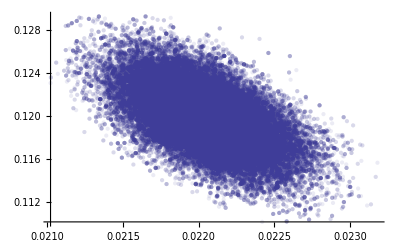

```mathematica
ListPlot[joint,PlotStyle->Opacity@0.1,PlotRange->All]
```

The joint plot using points is automated as

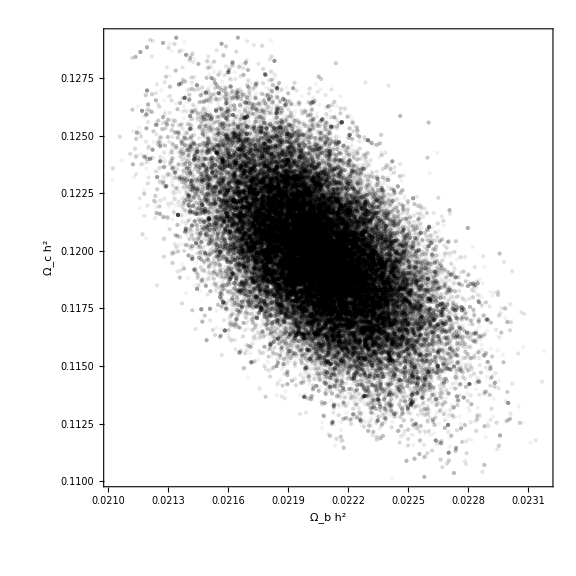

```mathematica
PlotSample[{"omegabh2","omegach2"}]
```

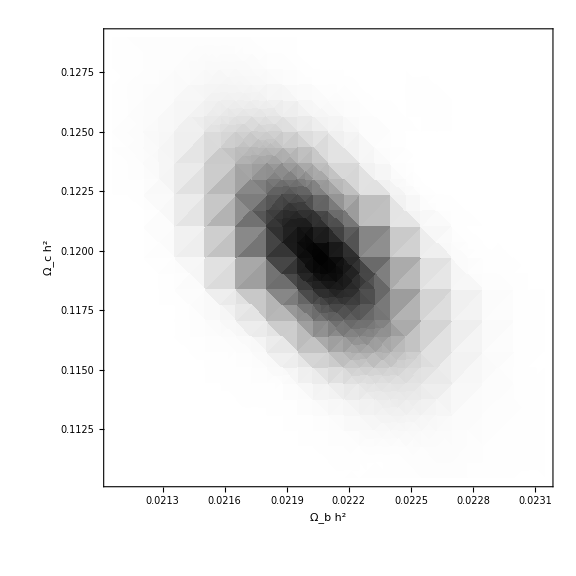

```mathematica
PlotDensity[{"omegabh2","omegach2"}]
```

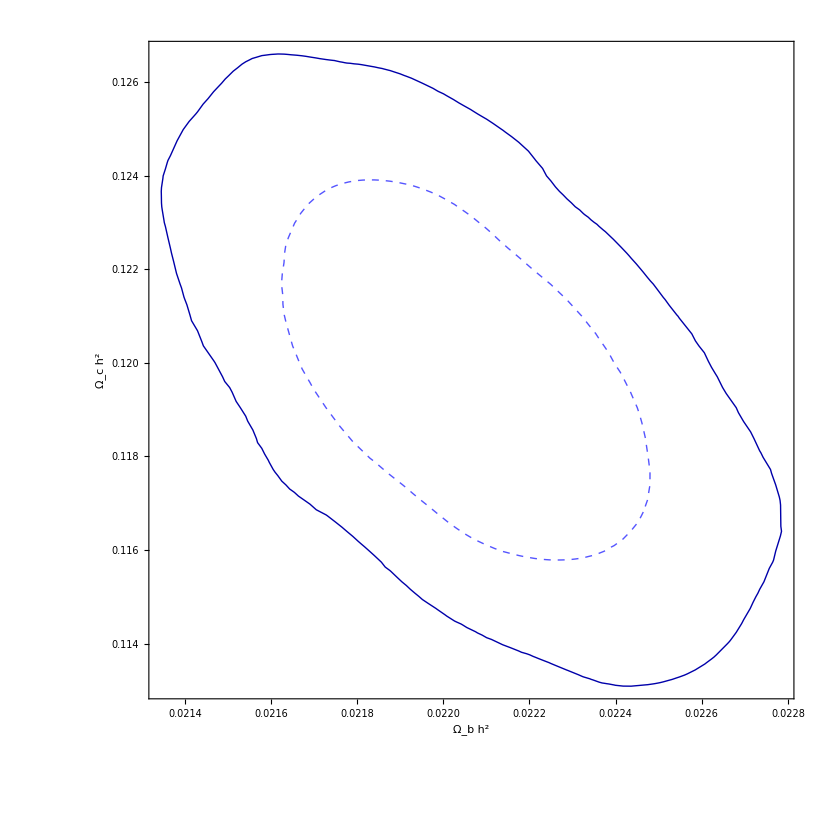

```mathematica
PlotContour[{"omegabh2","omegach2"}]
```

The -log(likelihood) = χ^2/2 can be selected using string “likelihood”.

```mathematica
2*Min[Sel["likelihood"]] (* This is the least χ^2 point in the Planck chain. Note that by minimizing χ^2 near this point in cosmomc, one can still get slightly lower χ^2. *)
```

9807.85

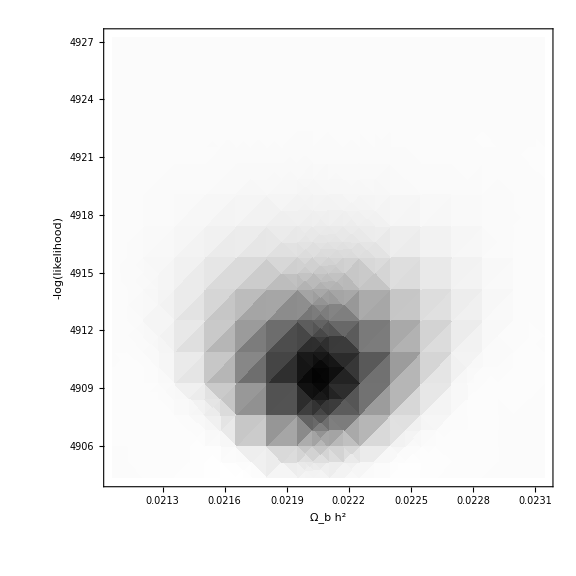

```mathematica
PlotDensity[{"omegabh2","likelihood"}]
```

The selection can be supplied with conditions

```mathematica
jointCut=Sel[{"omegabh2","omegach2"},"omegach2"<0.115||"omegach2">0.125];
```

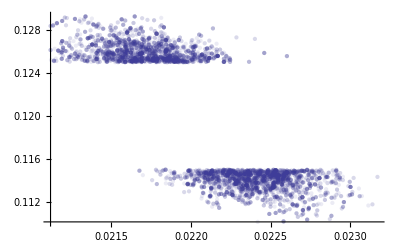

```mathematica
ListPlot[jointCut,PlotStyle->Opacity@0.1,PlotRange->All]
```

See how unprobable is “omegach2”<0.115

```mathematica
(Sel[{"omegach2"},"omegach2"<0.115]//Length)/(Sel[{"omegach2"}]//Length)//N
```

0.0329898

## Statistics plots

1d plot

Ω_c h^2 = 0.119838 ± 0.00268264 (mean, std var)

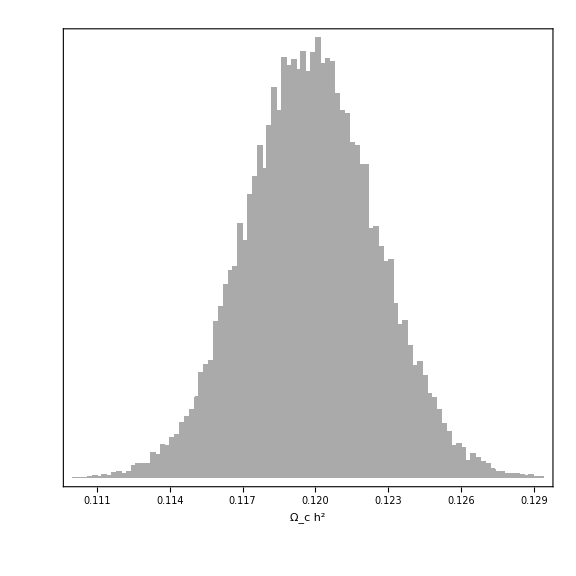

```mathematica
Stat["omegach2"]
```

2d statistics (currently only do PlotContour)

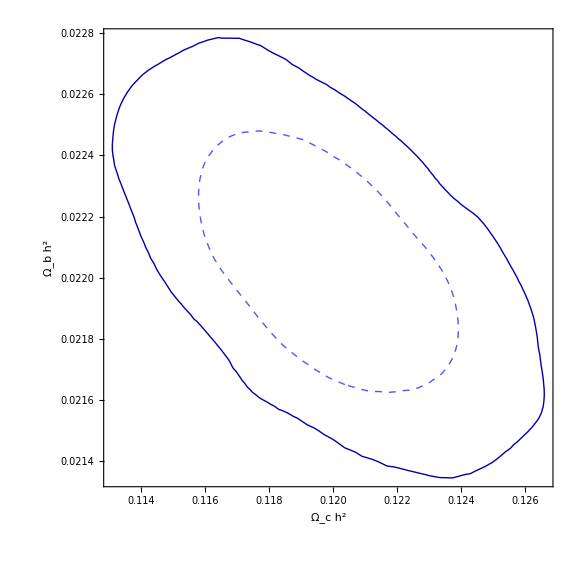

```mathematica
Stat[{"omegach2","omegabh2"}]
```

If colored contours are preferred:

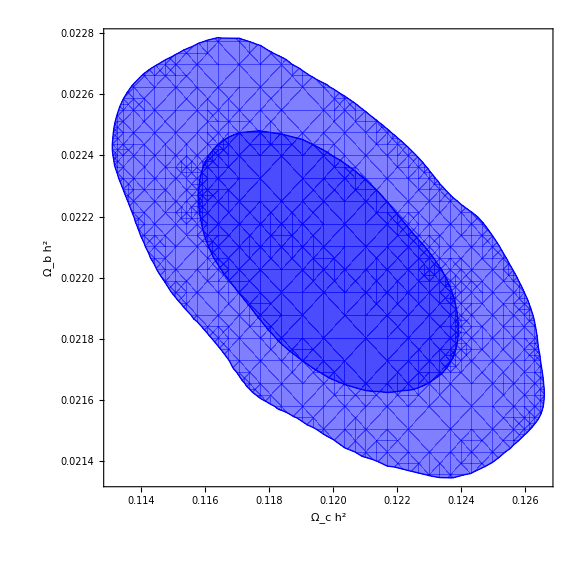

```mathematica
Stat[{"omegach2","omegabh2"},ContourShading->{None,Directive[Opacity@0.5,Blue],Directive[Opacity@0.7,Blue]},ContourStyle->Blue]
```

## Alternative chains

ChainStat using a global variable $Chain to store the chain to work on. Multiple sets of chains which can be combined can be loaded using LoadChain[{prefix1, prefix2, ...}]. 
On the other hand, if one wants to work on a completely different chain, one can use

Block[{$Chain=LoadChain[...], operations]

## Add derived parameters to chain

```mathematica
AddToChain["A", "P_\\zeta", 10^-10 Exp["logA"]];
```

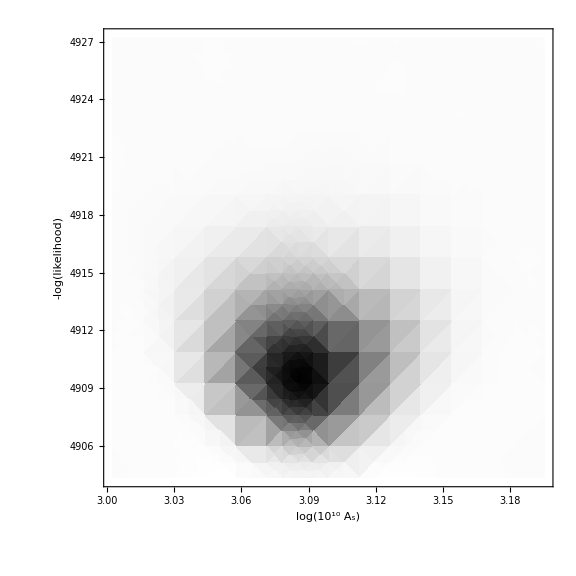

```mathematica
PlotDensity[{"logA", "likelihood"}]
```

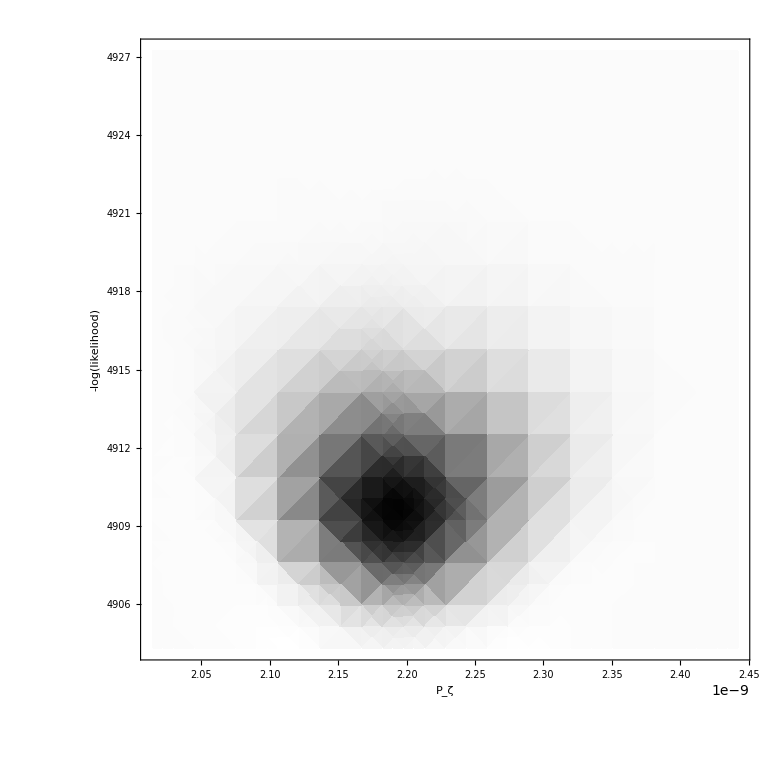

```mathematica
PlotDensity[{"A", "likelihood"}]
```